```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=0.2;
R=L/Sqrt[2];
c={L/2,h+L/2};
```

```mathematica
ra[t_]:={c[[1]]+R Cos[-3π/2 t+5π/4],c[[2]]+R Sin[-3π/2 t+5π/4]}
rb[t_]:=ra[t]+u[ra[t]]
```

```mathematica
u[r_]:={0, -r[[1]](r[[1]]-1)}
```

```mathematica
ua[x_]:=x^2-2
```

```mathematica
sa[t_]:=NIntegrate[Norm[ra'[s]],{s,0,t}]
sb[t_]:=NIntegrate[Norm[rb'[s]],{s,0,t}]
```

```mathematica
(*read u_a*)
ta=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/membrane/solution/u_a_test.csv"]
ta=Table[{ta[[i,5]],ta[[i,4]]},{i,2,Length[ta]}]
```

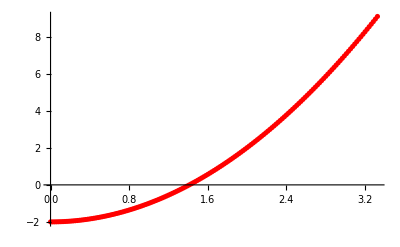

```mathematica
plotuanum=ListPlot[ta,PlotStyle->Red]
```

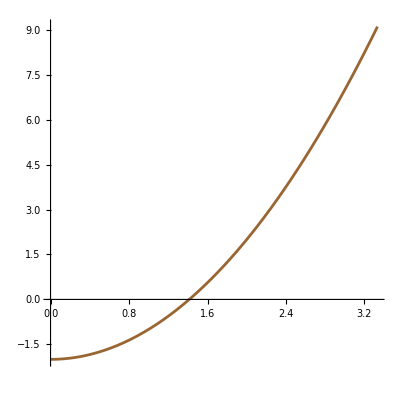

```mathematica
plotuaex=ParametricPlot[{sa[t],ua[sa[t]]},{t,0,1},PlotStyle->Brown,AspectRatio->1]
```

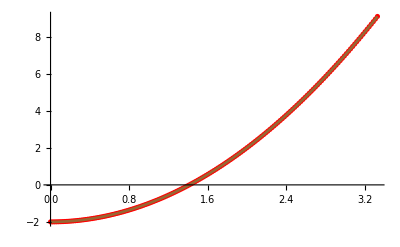

```mathematica
Show[plotuanum,plotuaex]
```

```mathematica
(*read u_b*)
```

```mathematica
tb=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/membrane/solution/u_b_test.csv"]
tb=Table[{tb[[i,5]],tb[[i,4]]},{i,2,Length[tb]}]
```

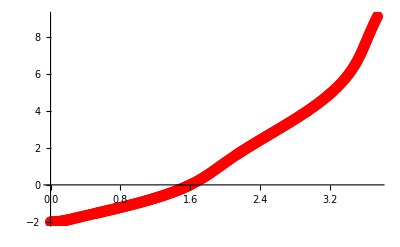

```mathematica
plotubnum=ListPlot[tb,PlotStyle->{Red,PointSize->.02}]
```

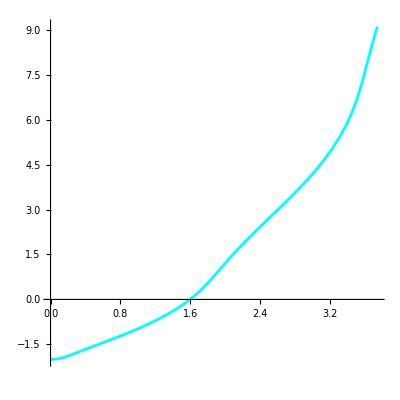

```mathematica
plotubex=ParametricPlot[{sb[t],ua[sa[t]]},{t,0,1},PlotStyle->Cyan,AspectRatio->1]
```

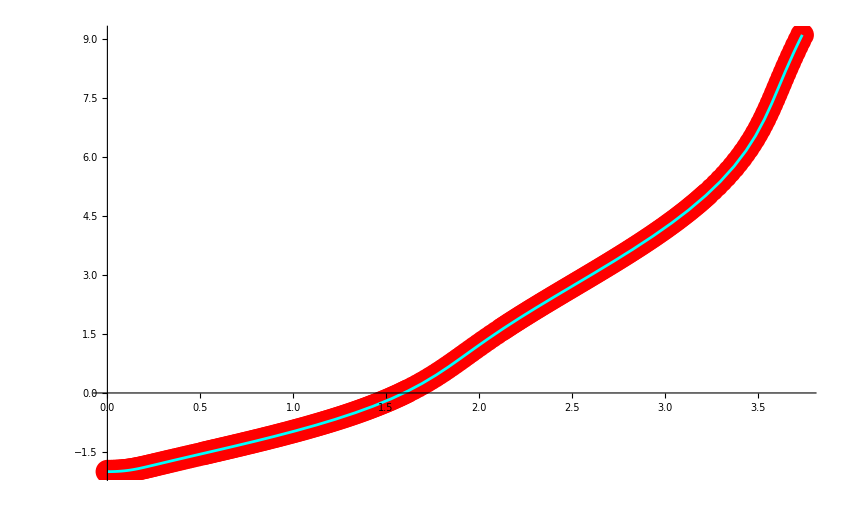

```mathematica
Show[plotubnum,plotubex]
```

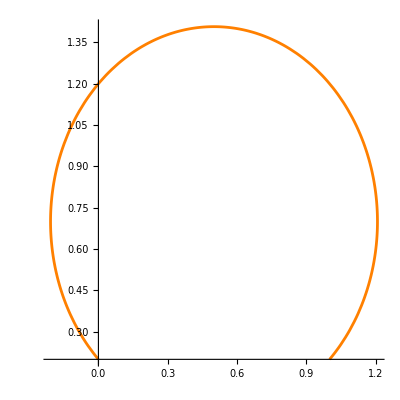

```mathematica
plotmesha=ParametricPlot[ra[t],{t,0,1},PlotStyle->Orange,AspectRatio->1]
```

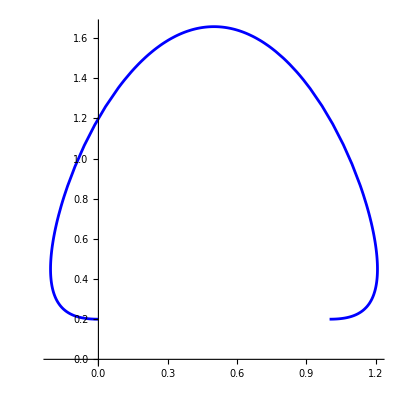

```mathematica
plotmeshb=ParametricPlot[ra[t]+u[ra[t]],{t,0,1},PlotStyle->Blue,AspectRatio->1]
```

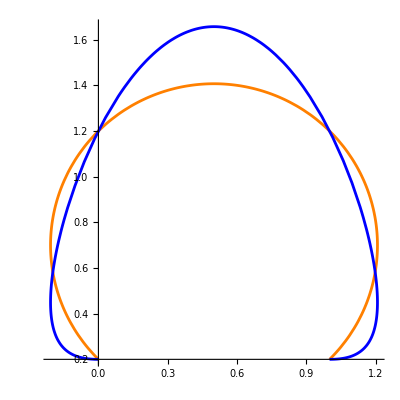

```mathematica
Show[plotmesha,plotmeshb,PlotRange->Full]
```

```mathematica
Show[plotua,plotub,PlotRange->Full]
```

Show::gcomb: Could not combine the graphics objects in Show[plotua,plotub,PlotRange→Full].

Show[plotua,plotub,PlotRange→Full]